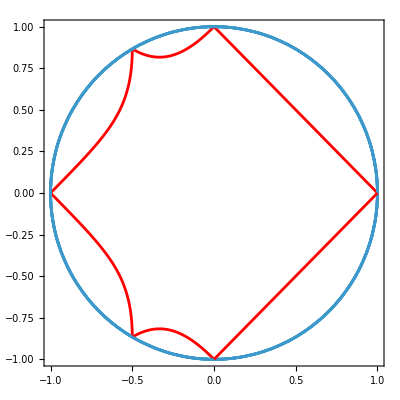

```mathematica
Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+((0.20998684164914552+0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)],
	   Im[-0.3333333333333333+((0.20998684164914552+0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ],  ParametricPlot[
	 {
	   Re[-0.3333333333333333+(0.41997368329829105+0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)],
	   Im[-0.3333333333333333+(0.41997368329829105+0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ], Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)+I α],
      Im[(1-α)+I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]
], Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+((0.20998684164914552-0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)],
	   Im[-0.3333333333333333+((0.20998684164914552-0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
], Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+(0.41997368329829105-0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)],
	   Im[-0.3333333333333333+(0.41997368329829105-0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
], Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)-I α],
      Im[(1-α)-I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]]
]
```

```mathematica
EE={}
randS=DiagonalMatrix[Table[0,{i,1,4}]];
S=DiagonalMatrix[Table[0,{i,1,4}]];For[k=1,k<100000,k++,For[i=1,i<=4,i++,For[j=1,j<=4,j++,randS[[i,j]]=RandomVariate[ChiSquareDistribution[0.1]]]];
For[i=1,i<=4,i++,For[j=1,j<=4,j++,S[[i,j]]=randS[[i,j]]/(randS[[1,j]]+randS[[2,j]]+randS[[3,j]]+randS[[4,j]])]];
EE=Union[EE,Eigenvalues[S]]]Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+((0.20998684164914552+0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)],
	   Im[-0.3333333333333333+((0.20998684164914552+0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ],  ParametricPlot[
	 {
	   Re[-0.3333333333333333+(0.41997368329829105+0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)],
	   Im[-0.3333333333333333+(0.41997368329829105+0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997-0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ], Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)+I α],
      Im[(1-α)+I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]
], Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+((0.20998684164914552-0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)],
	   Im[-0.3333333333333333+((0.20998684164914552-0.3637078786572404 ⅈ) (-4.+6. α))/((16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (16.-36. α+27. α^2+5.196152422706632 √(16. α^2-40. α^3+27. α^4))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
], Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-0.3333333333333333+(0.41997368329829105-0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)],
	   Im[-0.3333333333333333+(0.41997368329829105-0.7274157573144808 ⅈ)/((-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3))-(0.13228342099734997+0.22912160616643376 ⅈ) (-20.+27. α+5.196152422706632 √(16.-40. α+27. α^2))^(1/3)]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
], Show[
  ContourPlot[
    x^2+y^2==1,
    {x,-1,1},
    {y,-1,1},
    PlotRange->{{-1,1},{-1,1}}
  ],
  ParametricPlot[
    {
      Re[(1-α)-I α],
      Im[(1-α)-I α]
    },
    {α,0,1},
    PlotRange->{{-1,1},{-1,1}},
    AxesLabel->{"Re","Im"},
    PlotStyle->Red
  ]], ComplexListPlot[EE,PlotStyle->Red]
]
```

{}

Null -Graphics-